# Venn Diagram

### Author

Eric W. Weisstein
March 7, 2012

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Logic/VennDiagram.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/VennDiagram.html.

©2012 Wolfram Research, Inc. except for portions noted otherwise

### Initialization

```mathematica
<<Graphics`InequalityGraphics`
<<DiscreteMath`Combinatorica`
```

Get::noopen: Cannot open Graphics`InequalityGraphics`.

$Failed

Get::noopen: Cannot open DiscreteMath`Combinatorica`.

$Failed

### Code

```mathematica
VennDiagram[n_,ineqs_:{}]:=Module[{i,r=.6,R=1,v},
v=Table[Circle[r{Cos[#],Sin[#]}&[2Pi(i-1)/n],R],{i,n}];
{
If[ineqs=={},{},
InequalityPlot[(v/.Circle[{xx_,yy_},rr_]:>(x-xx)^2+(y-yy)^2<rr^2)[[ineqs]],
{x},{y},Axes->False,
Curves->None,
DisplayFunction->Identity][[1]]
],
v
}
]
```

## Diagram

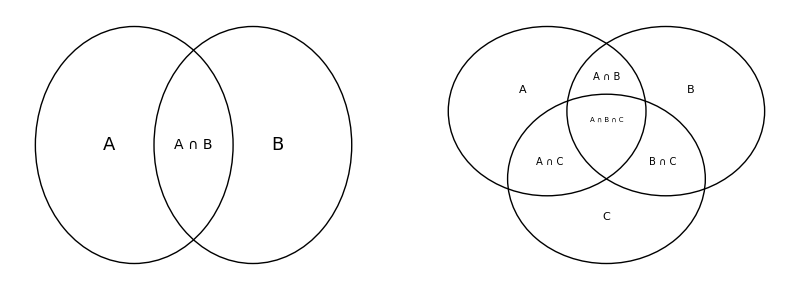

```mathematica
GraphicsRow[{
Graphics[{Circle[{-.6,0},1],Circle[{.6,0},1],
Text[Style["A",Italic,18],{-.85,0}],Text[Style["B",Italic,18],{.85,0}],Text[Style[Row[{Style["A",Italic]," ∩ ",Style["B",Italic]}],14],{0,0}]
}],
Graphics[{Circle[{-.6,0},1],Circle[{.6,0},1],Circle[{0,-.8},1],
Text[Style["A",Italic],{-.85,.25}],Text[Style["B",Italic],{.85,.25}],Text[Style["C",Italic],{0,-1.25}],
Text[Style[Row[{Style["A",Italic]," ∩ ",Style["B",Italic]}],10],{0,.4}],Text[Style[Row[{Style["A",Italic]," ∩ ",Style["C",Italic]}],10],{-.57,-.6}],Text[Style[Row[{Style["B",Italic]," ∩ ",Style["C",Italic]}],10],{.57,-.6}],
Text[Style[Row[{Style["A",Italic]," ∩ ",Style["B",Italic]," ∩ ",Style["C",Italic]}],7],{0,-.1}]
},BaseStyle->18]
}]//Quiet
```

## Diagrams

### n = 2

{{},{1},{2},{1,2}}

```mathematica
VennDiagram[n_,ineqs_: {}]:=Module[{i,r=.6,R=1,v,grouprules,x,y,x1,x2,y1,y2,ve},v=Table[Circle[r {Cos[#],Sin[#]}&[2 Pi (i-1)/n],R],{i,n}];
{x1,x2}={Min[#],Max[#]}&[Flatten@Replace[v,Circle[{xx_,yy_},rr_]:>{xx-rr,xx+rr},{1}]];
{y1,y2}={Min[#],Max[#]}&[Flatten@Replace[v,Circle[{xx_,yy_},rr_]:>{yy-rr,yy+rr},{1}]];
ve[x_,y_,i_]:=v[[i]]/.Circle[{xx_,yy_},rr_]:>(x-xx)^2+(y-yy)^2<rr^2;
grouprules[x_,y_]=ineqs/.Table[With[{is=i},Subscript[_,is]:>ve[x,y,is]],{i,n}];
Show[If[MatchQ[ineqs,{}|False],{},RegionPlot[grouprules[x,y],{x,x1,x2},{y,y1,y2},Axes->False]],Graphics[v],PlotLabel->TraditionalForm[Replace[ineqs,{}|False->∅]],Frame->False]]
```

```mathematica
TraditionalForm[And@@(Subscript[A,#]&/@#)]/.True->∅&/@Sort@Subsets[Range[4]]
```

{∅,A_1,A_2,A_3,A_4,A_1∧A_2,A_1∧A_3,A_1∧A_4,A_2∧A_3,A_2∧A_4,A_3∧A_4,A_1∧A_2∧A_3,A_1∧A_2∧A_4,A_1∧A_3∧A_4,A_2∧A_3∧A_4,A_1∧A_2∧A_3∧A_4}

ImplicitRegion::bcond: ∅ should be a Boolean combination of equations, inequalities, and Element statements.

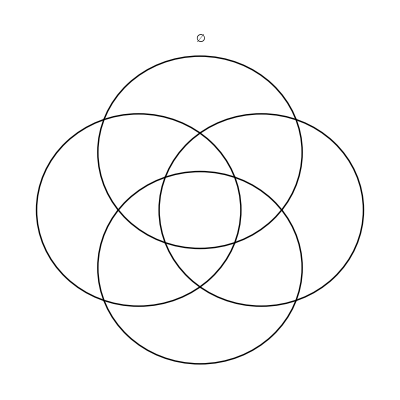
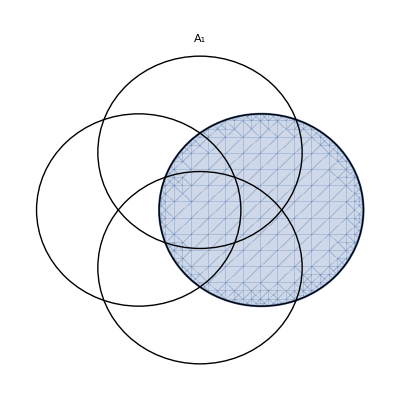
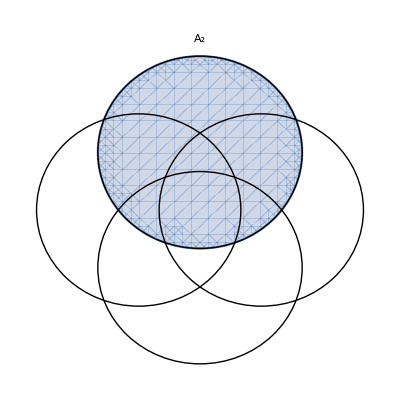
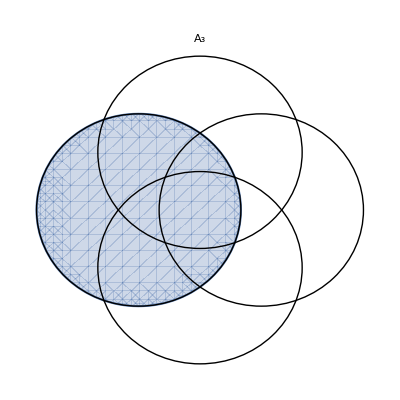
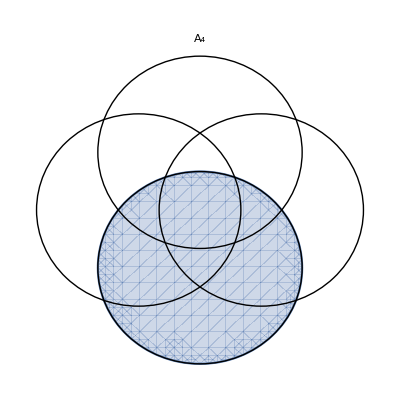
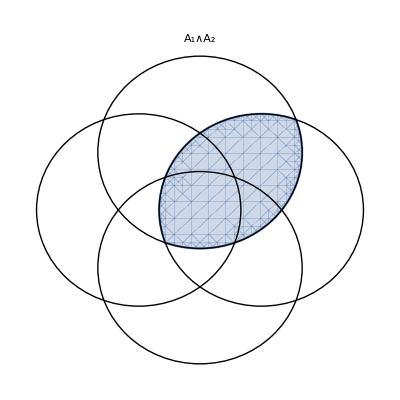
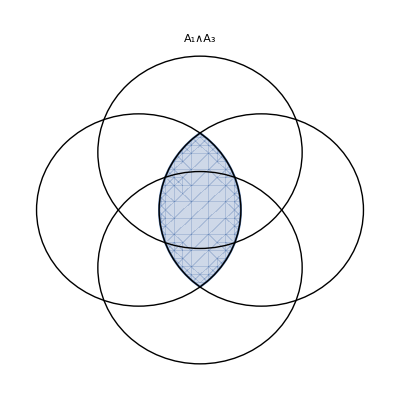
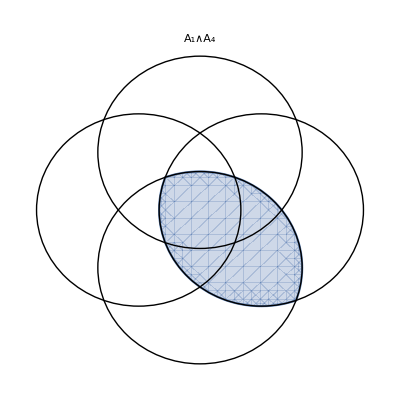

```mathematica
VennDiagram[4,#]&/@{∅,Subscript[A, 1],Subscript[A, 2],Subscript[A, 3],Subscript[A, 4],Subscript[A, 1]∧Subscript[A, 2],Subscript[A, 1]∧Subscript[A, 3],Subscript[A, 1]∧Subscript[A, 4],Subscript[A, 2]∧Subscript[A, 3],Subscript[A, 2]∧Subscript[A, 4],Subscript[A, 3]∧Subscript[A, 4],Subscript[A, 1]∧Subscript[A, 2]∧Subscript[A, 3],Subscript[A, 1]∧Subscript[A, 2]∧Subscript[A, 4],Subscript[A, 1]∧Subscript[A, 3]∧Subscript[A, 4],Subscript[A, 2]∧Subscript[A, 3]∧Subscript[A, 4],Subscript[A, 1]∧Subscript[A, 2]∧Subscript[A, 3]∧Subscript[A, 4]}
```

```mathematica
And[(Subscript[A,1]&&Subscript[A,2]),!(Subscript[A,3]&&Subscript[A,4])]//TraditionalForm
VennDiagram[4,%]
```

A_1∧A_2∧¬(A_3∧A_4)

```mathematica
And[Subscript[A,1],! Subscript[A,2], Subscript[A,3],! Subscript[A,4]]
```

A_1&&!A_2&&A_3&&!A_4

```mathematica
TableForm[BooleanTable[{A,Subscript[A, 1]&&!Subscript[A, 2]&&Subscript[A, 3]&&!Subscript[A, 4]},{A}],TableHeadings->{None,{A,Subscript[A, 1]&&!Subscript[A, 2]&&Subscript[A, 3]&&!Subscript[A, 4]}}]
```

A | A_1&&!A_2&&A_3&&!A_4
True | True_1&&!True_2&&True_3&&!True_4
False | False_1&&!False_2&&False_3&&!False_4

```mathematica
SatisfiabilityCount[Subscript[A, 1]&&!Subscript[A, 2]&&Subscript[A, 3]&&!Subscript[A, 4],{A}]
```

SatisfiabilityCount[A_1&&!A_2&&A_3&&!A_4,{A}]

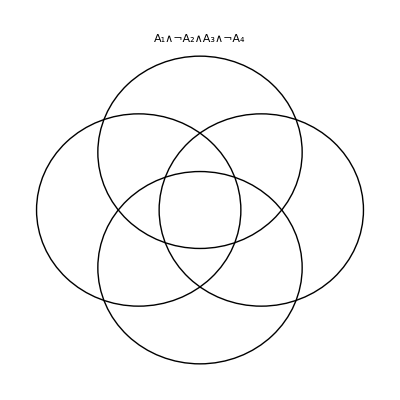

```mathematica
VennDiagram[4,Subscript[A, 1]&&!Subscript[A, 2]&&Subscript[A, 3]&&!Subscript[A, 4]]
```

### n = 3

```mathematica
Sort@Subsets[3]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Show[GraphicsArray[Partition[Graphics[VennDiagram[3,#],AspectRatio->Automatic,PlotLabel->TraditionalForm[And@@(Subscript[A,#]&/@#)]/.True->∅]&/@Sort@Subsets[3],4]
]]
```

⁃GraphicsArray⁃

### Doesn't work for n = 4

```mathematica
Show[Graphics[VennDiagram[4],AspectRatio->Automatic]]
```

⁃Graphics⁃

## Sums

### ∑_(k=0)^n Binomial[n, k]==2^n

```mathematica
Sum[Binomial[n,k],{k,0,n}]
```

2^n